## Physics 8.033 Fall 2016 - Optional Problem Set [100 pts]

## Due - 7 December 2016, 5:00 pm

## Instructions

Complete the notebook. Throughout the notebook, ... in code are incomplete parts for you to fill out. Some initial code snippets have already been written for you as a basic guide for what you should do, but you do not have to follow those snippets strictly! 

The parts marked SOLUTION will be graded, and typically will contain a print-out of some variable that you are asked to compute or contain a plot. Make sure that you have plotted/displayed the right thing in those cells. Some parts have Explanation: at the end, which is for you to write explanations or give numerical values. Please suppress all other outputs for ease of grading. Please produce all of the plots/print-outs required, and fill in all explanations in this notebook, and then submit the notebook online on the course website before the due date.

## Tips

Here are some common tips that you should know about before you start:

Code in Mathematica comes in cells. To execute the code in a cell, click on the cell (the square brackets on the right) and hit Shift + Enter. You can also select multiple cells to execute at a go.

Sometimes, Mathematica will try to perform a computation that you want to kill. You can do this by hitting Alt + . on your keyboard (or Apple + .). Sometimes you may need to press the keys multiple times for good effect.

Ending a line with ; suppresses the output. That saves clutter, but sometimes you might want to remove them to inspect the outcome of your code.

Variables marked in blue have not been defined (Mathematica doesn't know what it is yet), while variables marked in black are already defined.

Functions always start with a capital letter, e.g. Sin[x]. This is a common source of error for beginners, because Mathematica won’t report an error here: it will simply treat sin[x] as a bunch of mathematical symbols and happily go along with you.

In the following code block, after running all three cells in order sets b = 4. However, if you then decide to run the second and third cells again, it will now be 7! This is because all variables are global by default: changing the value of it anywhere, even in another notebook, changes the actual value of the variable. This is different from other programming languages you might be used to, and should always be the first thing to check when you run into mysterious bugs. The best thing to do is to go to Evaluation > Evaluate Notebook: I have included a line below that clears out all initialized variables and give you a clean slate before running all of the cells in order. You can also use the Clear command to manually reset individual variables.

```mathematica
b=1
```

1

```mathematica
b=b+1
```

2

```mathematica
b=b+2
```

4

The Mathematica documentation is extremely helpful. You will use it extensively, even after you’ve gotten reasonably experienced with the program. There is also plenty of support available online if you run into trouble. Mathematica Stack Exchange is one good place to look for solutions to any difficulty you may have.

Hartle is an excellent resource for the physics you are about to see below. You might want to spend some time reading the relevant portions of the book as you work through the problem set.

Don’t hesitate to approach either the TA or Prof. Slatyer for help, particularly if you’re stuck on some mysterious Mathematica bug or another. Piazza should be very useful for getting your questions answered promptly!

## About this Problem Set

In this problem set, we will determine the gravitational radiation produced by a body falling radially in a Schwarzschild metric. This is a drastically simpler calculation than the case of colliding, in-spiraling black holes, but it will (hopefully!) give you a taste of the physics involved.

## Clearing the values of symbols:

This line resets all initialized variables, giving you a clean slate. Read the list of common pitfalls and other weirdness at the end of your problem set for why this is important!

```mathematica
Remove["Global`*"];
```

## Defining a list of coordinates:

We will work in spherical coordinates for this problem. Special symbols are keyed in by typing \[...], where ... should be replaced by a keyword like Theta or CapitalDelta, for example.

```mathematica
coord = {t,r,θ,ϕ};
```

In this program indices range over 1 to n.  Thus for spacetime they range from 1 to 4, with 1 being the time index (Mathematica indices start at 1 instead of 0, which is unfortunate for any general relativity calculation!).

## (a) [10 pts] Manipulating Metrics in Mathematica

In this problem, we will study the Schwarzschild metric, which describes the spacetime geometry around a rotating black hole of mass M and angular momentum J. Setting c = G = 1, the metric is given by

ds^2=-(1-(2M)/r)dt^2 + (1-(2M)/r)^-1 dr^2+r^2(dθ^2+sin^2 θ dϕ^2)

### (i)

Enter the Schwarzschild metric with M=1 as a matrix called metric below, with rows (μ = t, r, θ, ϕ) and columns (ν =  t, r, θ, ϕ) corresponding to g_μν. As an example, the 2×2 identity matrix would be entered as {{1,0},{0,1}}. Remember to use Sin[θ], since we are interested in calling the actual function Sin later. You can choose other more convenient coordinate labels for the angular coordinates, or you can look up the documentation on “Greek Letters” to learn how to key them in. 

After you have successfully entered the metric, hit Shift + Enter. The last line of the code will display the metric as a matrix.

SOLUTION:

```mathematica
metric= DiagonalMatrix[{-(1-2/r), (1-2/r)^-1, r^2, r^2 Sin[θ]^2}];
metric//MatrixForm
```

(-1+2/r | 0 | 0 | 0
0 | 1/(1-2/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

### (ii)

The inverse metric is obtained through matrix inversion. Look up the function for taking an inverse, and use Simplify where necessary. Once again, the last line of the code will display inversemetric in matrix form.

SOLUTION:

```mathematica
inversemetric= Simplify[Inverse[metric]];
inversemetric//MatrixForm
```

(r/(2-r) | 0 | 0 | 0
0 | (-2+r)/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2)

## (b) [30 pts] Christoffel Symbols and Radial Trajectory

### (i)

Calculate the Christoffel symbols. Store your results as a list called affine, with affine[[i,j,k]] being the Christoffel symbol  (Γ^i)_jk=1/2 g^im(∂_j g_mk+∂_k g_mj-∂_m g_jk). You should find the following Mathematica functions useful: D for taking partial derivatives, Sum for summing over repeated indices, Table for forming a list of components, and Simplify for simplifying the result. Running the next cell will output affine in a readable fashion.

SOLUTION:

```mathematica
affine= Simplify[Table[1/2 Sum[inversemetric[[i, m]] (D[metric[[m, k]], coord[[j]]] + D[metric[[m, j]], coord[[k]]] - D[metric[[j, k]], coord[[m]]]),{m, 1, 4}], {i, 1, 4}, {j, 1, 4}, {k, 1, 4}]];
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}] ,{i,1,4},{j,1,4},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 1] | 1/((-2+r) r)
Γ[2, 1, 1] | (-2+r)/r^3
Γ[2, 2, 2] | 1/(2 r-r^2)
Γ[2, 3, 3] | 2-r
Γ[2, 4, 4] | -(-2+r) Sin[θ]^2
Γ[3, 3, 2] | 1/r
Γ[3, 4, 4] | -Cos[θ] Sin[θ]
Γ[4, 4, 2] | 1/r
Γ[4, 4, 3] | Cot[θ]

### (ii)

We will now solve the geodesic equations numerically for the Schwarzschild metric. First, we will set θ = π/2, so that we are only dealing with equatorial solutions here:

```mathematica
affine=affine/.θ->π/2;
```

Next, we need to make sure that affine is an explicit function of τ, so that Mathematica knows that τ is the independent variable of the equation. To do this, we do the following:

```mathematica
affine=affine/.r->r[τ];
```

This replaces every instance of r in affine with r[τ].

We will now write all 4 geodesic equations as a list using the function Table. Complete the expression below: you may find the function Sum useful. Also take a look at the function NDSolveValue for examples of how to write differential equations in Mathematica: we will use NDSolveValue later to solve these equations to get the radial trajectory.

SOLUTION:

```mathematica
geod = Simplify[Table[coord[[i]]''[τ] + Sum[affine[[i, j, k]] coord[[j]]'[τ] coord[[k]]'[τ], {j, 1, 4}, {k, 1, 4}] == 0,{i, 1, 4}]]
```

{(2 r'[τ] t'[τ])/((-2+r[τ]) r[τ])+t''[τ]==0,r'[τ]^2/(2 r[τ]-r[τ]^2)+((-2+r[τ]) t'[τ]^2)/r[τ]^3+r''[τ]==(-2+r[τ]) (θ'[τ]^2+ϕ'[τ]^2),(2 r'[τ] θ'[τ])/r[τ]+θ''[τ]==0,(2 r'[τ] ϕ'[τ])/r[τ]+ϕ''[τ]==0}

### (iii)

To solve the geodesic equations, we have to first specify some initial conditions. We are solving 4 second-order differential equations, so we’ll need 8 conditions: the initial value of each coordinate, and their derivatives with respect to proper time. 

Complete the initial conditions for a particle at r=1000 (since G=1 and M=1, this is equivalent to 1000 times the Schwarzschild radius), starting at rest, following the syntax for the θ initial conditions as an example. Print out initCond for grading. Be careful about how you obtain the initial condition for t'≡dt/dτ ! Explain how you would use the metric tensor to get this condition.

SOLUTION:

```mathematica
initCond={
coord[[1]][0]==0,coord[[1]]'[0]==√(-inversemetric[[1, 1]]/.r->1000),
coord[[2]][0]== 1000,coord[[2]]'[0]== 0,
coord[[3]][0]==π/2,coord[[3]]'[0]==0,
coord[[4]][0]==0,coord[[4]]'[0]==0
}
```

{t[0]==0,t'[0]==10 √(5/499),r[0]==1000,r'[0]==0,θ[0]==π/2,θ'[0]==0,ϕ[0]==0,ϕ'[0]==0}

Explanation: We know u^μ u_μ = -1. Since the particle starts at rest, u^r[0] = u^θ[0] = u^ϕ[0] = 0. Since the metric is diagonal, u^μ[0]u_μ[0] = (u^t)^2 g_tt=-1 → u^t = √(-g^tt). Thus t’[τ=0] = √(-g^tt)evaluated at r = r[0] = 1000.

### (iv)

The 4 equations in geod and the 8 initial conditions in initCond can now be combined a solved numerically using the function NDSolveValue. Look up this function in the documentation if you haven’t already done so, and integrate these equations to τ=35122. You may find the function Join helpful.

SOLUTION:

```mathematica
soln=NDSolveValue[Join[geod, initCond], coord, {τ, 0, 35122}];
```

### (v)

The object soln should now be a list of 4 objects, each of type InterpolatingFunction: these are essentially the solutions for t, r, θ and ϕ respectively. To find r at proper time τ=5 for example, we would write soln[[2]][5] to get the second interpolating function in the list and evaluate it at 5. 

Use Table to form a list of pairs (t,r), starting from τ=0, τ=1, ... to τ=35122, i.e. with Δτ = 1. This should look something like {{t(τ=1),r(τ=1)},{t(τ=2),r(τ=2)}...{t(τ=35122),r(τ=35122)}}.

```mathematica
radTrajRel= Table[{soln[[1]][i], soln[[2]][i]}, {i, 0, 35122}];
```

### (vi)

In Newtonian gravity, what should we expect the trajectory to be? Make a similar table as radTrajRel for the t and r coordinate, called radTrajClas, from t=0, t=1 ... to t=35122, i.e. with Δt = 1. To find this trajectory, you can use NDSolveValue once again with an appropriate differential equation and initial conditions. Plot both tables on the same plot, plotting the Newtonian trajectory in red and the relativistic trajectory in blue. Explain what you should see in your plot both far away from the Schwarzschild radius and near it.

You may find ListPlot and Show helpful for this part of the question.

SOLUTION:

```mathematica
solnNewt=NDSolveValue[{r''[t]+1/r[t]^2==0, r[0]==1000, r'[0]==0}, r, {t, 0, 35122}];
```

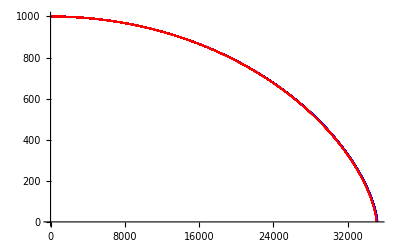

```mathematica
radTrajClas = Table[{i, solnNewt[i]}, {i, 0, 35122}];
Show[ListPlot[{radTrajRel, radTrajClas}, PlotStyle->{Blue, Red}]]
```

Explanation: Far away from the Schwarzschild radius (r=2), we should see the relativistic result approximately equal to the Newtonian result. But as t increases, the relativistic plot should asymptotically approach r = 2 (i.e. it takes a infinite time for the particle to fall past the event horizon from an outside observer), whereas the Newtonian plot will continue as it was.

## (c) [30 pts] Gravitational Radiation Loss from Infall

We will now calculate the total gravitational power emitted by the radial infall, assuming that we are in the far-field and also assuming non-relativistic motion of the infalling particle. Sections 23.4 and 23.6 in Hartle should be helpful for this part of the problem.

### (i)

Starting from the second mass moment (equation 23.34), obtain the quadrupole moment tensor (defined in equation 23.50 of Hartle). Save this as a 3×3 array. You may take the infalling particle to have mass m = 1 (as a result, any energy quantities here are calculated in units of m), and the radial direction in which it is falling to be the z-direction, so that the quadrupole moment tensor should be a function of z[t].

SOLUTION:

```mathematica
secondMassMom={{0, 0, 0}, {0, 0, 0}, {0, 0, z[t]^2}};
quadMomTensor=Table[secondMassMom[[i, j]]-1/3 KroneckerDelta[i, j]Sum[secondMassMom[[k, k]], {k, 1, 3}], {i, 1, 3}, {j, 1, 3}]
```

{{-1/3 z[t]^2,0,0},{0,-1/3 z[t]^2,0},{0,0,(2 z[t]^2)/3}}

### (ii)

Calculate the total energy lost as gravitational radiation for the Newtonian trajectory numerically. First, calculate the power lost, GWLossPower, as a function of z[t]. Then, integrate the power lost over time to get GWLoss. Do not worry about time-averaging: integrating over the time for the infall averages over many cycles of the radiation, and so effectively takes into account the time average.
Hint: You may find the function D to be helpful for taking derivatives. Since quadMomTensor is defined assuming a trajectory z[t], you can use the function /. to replace z with solnNewt. Make sure to show the output for the total energy lost. You may find NIntegrate to be a useful function here.

SOLUTION:

```mathematica
GWLossPower= Simplify[1/5 Sum[D[quadMomTensor[[i, j]], {t, 3}]^2, {i, 1, 3}, {j, 1, 3}]];
GWLoss=NIntegrate[GWLossPower/.z->solnNewt, {t, 0, 35122}]
```

0.00707901

### (iii)

Calculate the total energy lost as gravitational radiation GWLossatR for the Newtonian trajectory of a particle starting from infinity to some radius R analytically, and check that your answer agrees well with your result in (i) by outputting the total power loss (from the analytic result) at the end of the trajectory saved in solnNewt. For a mass falling to the Schwarzschild radius from infinity, what fraction of the mass GWLossatRs is radiated as gravitational waves? Output the functional form of the total energy lost, your comparison with (i) and the fraction as part of your solution.

Hint: start from the functional form of GWLossPower as a function of z[t] and, using what you know from classical mechanics to write all derivatives of z in terms of z. Finally, note that when you perform the integral, dt=dz/ż. You will find both /. and Integrate useful here.

SOLUTION:

```mathematica
GWLossPower=GWLossPower/.{z'[t]->√(2/z[t]),z''[t]->-1/z[t]^2, z'''[t]->√(2/z[t])2/z[t]^3};
Print["Total energy lost: ", GWLossatR=Assuming[R>0,Integrate[GWLossPower √(z[t]/2), {z[t], R, ∞}]]];
Print["Comparison:"];
Print["    Last time: ", GWLoss];
Print["    This time: ", Simplify[GWLossatR /.R->solnNewt[35122]]];

Print["Fractional loss: ", GWLossatRs= GWLossatR /.R->2];
```

Total energy lost: (16 √2)/(105 R^(7/2))

Comparison:

Last time: 0.00707901

This time: 0.00703871

Fractional loss: 2/105

## (d) [30 pts] Radiation Spectrum and Waveform

We will now calculate the expected spectrum of gravitational waves from the infall in the Newtonian approximation, using the analytic result you just derived. To do this, we will need to do some Fourier analysis. 

The main premise of Fourier analysis is that any signal (E-fields, gravitational waves, etc.) f(t) that is a function of t can be decomposed into a sum of sinusoidal signals, with sinusoids at each frequency ω weighted according to some function f̃(ω), so that

f(t)=1/(√(2π))(∫_(-∞))^∞f̃(ω)e^iωt dt

This is a very rich area in mathematics and is ubiquitous in quantum mechanics, but the main result we need to know here is known as Parseval’s theorem. Typically, the power loss P of in a wave is related to the square of the amplitude of the wave. If we can write P=|f(t)|^2, then Parseval’s theorem states that

E=(∫_(-∞))^∞|f(t)|^2 dt=1/(2π)(∫_(-∞))^∞|f̃(ω)|^2 dω

### (i)

Compute GWLossatt, the energy lost due to gravitational radiation as a function of time t, the time taken for the infall in the Newtonian case. Use the analytic results from the previous part, and again assume radial infall along the z-axis. We will now change the convention for timing so that t=0 when the particle reaches the origin at z=0: this means that infall will occur for negative values of t. You can obtain GWLossatt by solving for z as a function of t (call this zInTermsOft), and substituting that expression into GWLossatR. Output the function. You may find DSolveValue and /. useful here.

SOLUTION:

```mathematica
zInTermsOft= DSolveValue[{z[t] z'[t]^2 == 2, z[0]==0}, z[t], t];
GWLossatt= GWLossatR /.R-> zInTermsOft
```

DSolveValue::dsvb: There are multiple solution branches for the equations, but DSolveValue will return only one. Use DSolve to get all of the solution branches.

(32 2^(2/3))/(945 3^(1/3) (-t)^(7/3))

### (ii)

Take the time derivative of GWLossatt to get the power loss to get GWLossPowerTimeDom. Output the function. Verify that your expression for the power loss is proportional to (-t)^(-10/3).

SOLUTION:

```mathematica
GWLossPowerTimeDom= D[GWLossatt, t]
```

(32 2^(2/3))/(405 3^(1/3) (-t)^(10/3))

### (iii)

We will now use Parseval’s theorem to obtain |f(ω)|^2. First, note that the Fourier transform goes from t=-∞ to t=∞, but we are really only interested in t<0 here. We therefore want to set GWLossPowerTimeDom for t>0 to be zero. This can be done by multiplying GWLossPowerTimeDom by the step function, HeavisideTheta[-t] before applying the transform. Output the final form of f(t)=√(P(t)).

SOLUTION:

```mathematica
fTimeDom= √(GWLossPowerTimeDom *HeavisideTheta[-t])
```

(4 2^(5/6) √(HeavisideTheta[-t]/(-t)^(10/3)))/(9 3^(1/6) √5)

### (iv)

Perform the Fourier transform on fTimeDom to get fFreqDom, which is f̃(ω). Obtain |f̃(ω)|^2, called engLossSpectrum below. Output engLossSpectrum.

SOLUTION:

```mathematica
fFreqDom = FourierTransform[fTimeDom, t, ω];
engLossSpectrum= Simplify[fFreqDom Conjugate[fFreqDom], ω∈ Reals]
```

(4 2^(2/3) Abs[ω]^(4/3) Gamma[-2/3]^2 (-ⅈ+√3 Sign[ω]) (ⅈ+√3 Sign[ω]))/(405 3^(1/3) π)

### (v)

Right now, engLossSpectrum is a function of both positive and negative frequencies. We will manipulate engLossSpectrum so that it returns the power in both positive and negative frequencies as a function of just the positive frequency. 

Check that engLossSpectrum is symmetric between ω and -ω, even though the form of your answer may depend on Sign[ω]. Remove Sign[ω] from the expression for 	engLossSpectrum (since it does not depend on the sign), and multiply by 2, to account for the power in the negative frequencies. Output the new engLossSpectrum.

SOLUTION:

```mathematica
engLossSpectrum= 2  Simplify[engLossSpectrum/.Sign[ω] -> 1]
```

(32 2^(2/3) Abs[ω]^(4/3) Gamma[-2/3]^2)/(405 3^(1/3) π)

### (vi)

The energy loss spectrum that you should have obtained is proportional to ω^α, for some real number α. Give the value of α.

Explanation: α = 4/3.

The energy loss spectrum obviously cannot grow arbitrarily with frequency, as that would give infinite energy! Explain what you might expect to see in a fully general relativistic calculation. At what frequency do you expect the power spectrum from the classical trajectory to start differing significantly from the GR result? Explain your reasoning.

Explanation: The power spectrum has the same functional form at low frequencies, but above a certain characteristic frequency ω_0, the spectrum should decay to zero. ω_0∼c/R_s. This makes sense, since the classical trajectory is not sensitive to relativistic effects that occur at the length scale of R_s, and hence we expect the classical and the relativistic effects to differ at wavelengths shorter than R_s, or frequencies higher than c/R_s.

### (vii)

As you saw in the last part, the spectrum will rise up to an angular frequency ω_0, determined by the breakdown of the Newtonian approximation and the need to account for GR effects. ω_0 is thus the characteristic angular frequency of the gravitational waves where the spectrum peaks. 

Estimate f_0=ω_0/2π for gravitational radiation produced by a Schwarzschild black hole with a mass of 30 solar masses, and another mass falling radially into the black hole. Output your answer in Hz. Remember that we have thus far been working in units where G=M=m=1, so be careful when restoring the appropriate units! You can compare your result to the frequency of signals received at LIGO to see that the result we get is somewhere in the ball park, although of course the physics of black hole mergers is significantly more complicated!

SOLUTION:

```mathematica
G = 6.67*10^-11; M = 30*1.989*10^30;c = 3*10^8; Subscript[r, s] = (2 G M)/c^2;Subscript[ω, 0] = c/Subscript[r, s];
f0=Subscript[ω, 0]/(2π)
```

539.849